```mathematica
SetDirectory[NotebookDirectory[]];
CvData = Import["8_cv.dat","Table"];
MagnetData = Import["8_magnetization.dat","Table"];
SusceptData = Import["8_susceptibility.dat","Table"];
```

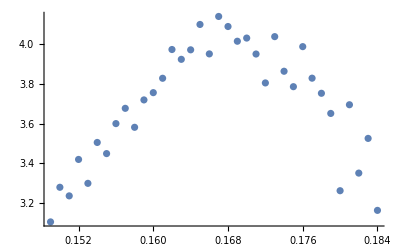

```mathematica
ListPlot[Take[SusceptData,{150,185}], PlotRange->Full]
```

```mathematica
SusceptFit = NonlinearModelFit[Take[SusceptData,{150,185}],A*Exp[-( x-mu)^2/(2 Sigma^2)],{{A,4},Sigma,mu},x];
```

```mathematica
SusceptFit[{"BestFit","ParameterTable"}]
```

{4.01441 ⅇ^(-762.526 (-0.167801+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 4.01441 | 0.0280584 | 143.074 | 1.12253×10^-47
Sigma | -0.0256069 | 0.000897353 | -28.5361 | 7.76798×10^-25
mu | 0.167801 | 0.000339012 | 494.969 | 1.87442×10^-65}

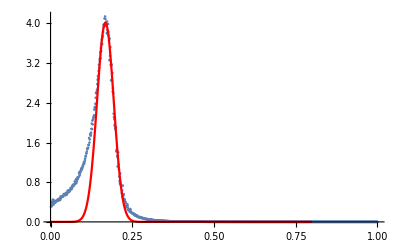

```mathematica
Show[ListPlot[SusceptData, PlotRange->Full],Plot[SusceptFit[x],{x,0,0.8},PlotRange->{{0,0.8},{0,500}}, PlotStyle->Red]]
```

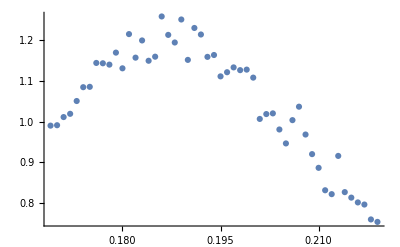

```mathematica
ListPlot[Take[CvData,{170,220}]]
```

```mathematica
CvFit = NonlinearModelFit[Take[CvData,{160,220}],A*Exp[-( x-mu)^2/(2*Sigma^2)],{A,Sigma,mu},x]
```

FittedModel[1.19276 ⅇ^(-562.104 (-«20»+x)^2)]

```mathematica
CvFit[{"BestFit","ParameterTable"}]
```

{1.19276 ⅇ^(-562.104 (-0.188144+x)^2), | Estimate | Standard Error | t-Statistic | P-Value
A | 1.19276 | 0.00734462 | 162.399 | 8.25539×10^-79
Sigma | 0.0298247 | 0.000484278 | 61.586 | 1.51303×10^-54
mu | 0.188144 | 0.000260553 | 722.094 | 2.28014×10^-116}

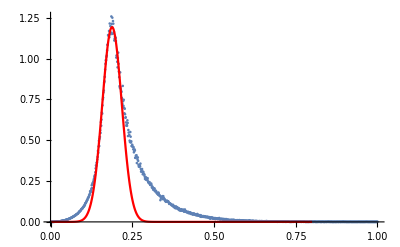

```mathematica
Show[ListPlot[CvData, PlotRange->Full],Plot[CvFit[x],{x,0,0.8},PlotRange->Full,PlotStyle->Red]]
```